## Object and transformations

### The shape and definitions

```mathematica
shape00:=Rectangle[{-1,-1},{1,1}];
shape01:= Triangle[{{-1,-1},{1,-1},{0,√3-1}}];
gt[x___]:=GeometricTransformation[x];
rt[x___]:=RotationTransform[x];
tt[x___]:=TranslationTransform[x];
```

#### Testing

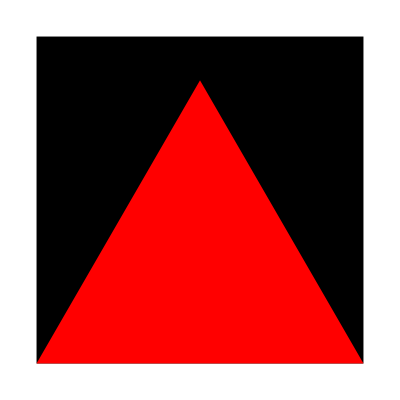

```mathematica
Graphics[{{shape00},{Red,shape01}}];
```

### Transformations

Transpose table

```mathematica
n=8;m=8;muloff=2.85;
(*tab[t_]:= Flatten[Table[{muloff*i+t,muloff*j},{i,-n,n},{j,-m,m}],1];*)
tab[t_]:=Flatten[Table[RotationMatrix[t].{muloff*i,muloff*j},{i,-n,n},{j,-m,m}],1]
rotarg[x_,y_]:=Sin[(x+y)/10];
(*rotarg[x_,y_]:=Sin[x*y/5^2];*)
traarg[x_,y_]:={x,y};

GeoTrans[g_,pt_]:= GeometricTransformation[g,
Composition[
	TranslationTransform[Apply[traarg,pt]],
	RotationTransform[Apply[rotarg,pt]]
]]
```

#### Testing

```mathematica
Map[GeoTrans[shape00,#]&,tab[2]]
```

#### Testing Graphics

```mathematica
Manipulate[Graphics[
Map[GeoTrans[shape00,#]&,tab[t]],
Axes->True,
PlotRange->{{-4π,4π},{-4π,4π}}
],{t,0,π/2}]
```

## Exports

#### the plus

```mathematica
gif=Table[Graphics[
Map[GeoTrans[shape00,#]&,tab[t]],
Axes->False,
PlotRange->{{-4π,4π},{-4π,4π}}
],{t,0,2.85,2.85/(1*50)}];
Export["plusxy.gif",gif,"DisplayDurations"->0.02]
```

plusxy.gif

#### the mul

```mathematica
gif=Table[Graphics[
Map[GeoTrans[shape00,#]&,tab[t]],
Axes->False,
PlotRange->{{-4π,4π},{-4π,4π}}
],{t,0,2.85,2.85/(1*50)}];
Export["multxy.gif",gif,"DisplayDurations"->0.02]
```

multxy.gif

#### the rot

```mathematica
tab[t_]:=Flatten[Table[RotationMatrix[t].{muloff*i,muloff*j},{i,-n,n},{j,-m,m}],1]
gif=Table[Graphics[
Map[GeoTrans[shape00,#]&,tab[t]],
Axes->False,
PlotRange->{{-4π,4π},{-4π,4π}}
],{t,0,π/2,π/2/(1*50)}];
Export["rotplusxy.gif",gif,"DisplayDurations"->0.02]
```

rotplusxy.gif